Dynamic simulation of three-wheeled omnidirectional mobile robot

```mathematica
Clear["Global`*"];
```

## Section I.

### Initialization

```mathematica
initialPos={0,0,0,0};
```

```mathematica
aaa=14.5/100;
L=aaa/0.8/√3
R=0.8 L;
wR=0.03;
wW=0.025;
mW=0.06;
ρ=7850;
γA=π/6; γB=γA+(2π)/3;γC=γB+(2π)/3;
A=({{-Sin[γA], Cos[γA], L}, {-Sin[γB], Cos[γB], L}, {-Sin[γC], Cos[γC], L}});
```

0.104645

```mathematica
heightCase=0.008;
h=heightCase;
rSC={0,0,heightCase/2};
mCase=R^2 π heightCase ρ
```

1.38269

```mathematica
heightPackage = 0.05;
pR=0.3 R;
rSP={0,0,heightCase/2+heightPackage/2};
mPackage=pR^2 π heightPackage ρ
```

0.777762

```mathematica
rS=rSC;
rS=(rSC mCase+rSP mPackage)/(mCase+mPackage)
```

{0.,0.,0.013}

```mathematica
ux={1,0,0};
uy={0,1,0};
uz={0,0,1};
rO={0,0,0};

uxA=RotationMatrix[γA,{0,0,1}].ux;
uxB=RotationMatrix[γB,{0,0,1}].ux;
uxC=RotationMatrix[γC,{0,0,1}].ux;
uyA=RotationMatrix[γA,{0,0,1}].uy;
uyB=RotationMatrix[γB,{0,0,1}].uy;
uyC=RotationMatrix[γC,{0,0,1}].uy;
uzA=Cross[uxA,uyA];
uzB=Cross[uxB,uyB];
uzC=Cross[uxC,uyC];
rA=L uxA;
rB=L uxB;
rC=L uxC;
```

### 3 D model of the robot and its environment

#### Draw functions

```mathematica
DrawRobot[{x_,y_,z_,φ_}]:={EdgeForm[Black],
Translate[
Rotate[
{
Red,Sphere[rO,L/100],
Pink,Opacity[0.8],
Cylinder[{rA-wW/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wW/2 (Normalize[rA][[1;;2]]~Join~{0})},wR],
Cylinder[{rB-wW/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wW/2 (Normalize[rB][[1;;2]]~Join~{0})},wR],
Cylinder[{rC-wW/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wW/2 (Normalize[rC][[1;;2]]~Join~{0})},wR],
Gray,Thick,Opacity[1],
	Line[{0.8 rA,rA}],
	Line[{0.8 rB,rB}],
	Line[{0.8 rC,rC}],
Cyan,Opacity[0.6],
Cylinder[{rO-heightCase/2 uz,rSC+heightCase/2 uz},R],
Black,Opacity[0.6],EdgeForm[White],
Cylinder[{rSC+heightCase/2 uz,rSC+heightCase/2 uz+heightPackage uz},pR],

},φ,{0,0,1}],{x,y,z}]}
```

```mathematica
DrawGround={EdgeForm[Black],
planeSize=60 L;
Gray,Yellow,Polygon[{{-planeSize L,-planeSize L,-wR},{-planeSize L,planeSize L,-wR},{planeSize L,planeSize L,-wR},{planeSize L,-planeSize  L,-wR}}]
};
```

```mathematica
DrawGlobalAxes[{x_,y_,z_,φ_}]:={EdgeForm[Black],
Translate[
{
Gray,
	Line[{rO,ux planeSize/13}],Text["x",1.2ux planeSize/13],
	Line[{rO,uy planeSize/13}],Text["y",1.2uy planeSize/13],
	Line[{rO,uz planeSize/13}],Text["z",1.2uz planeSize/13],

},{x,y,z}]}
```

#### Draw the environment

```mathematica
initialPos={0,0,0,0};
Graphics3D[
DrawRobot[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround,
AxesLabel->{x,y,z},Axes->{True, True, True}]
```

-Graphics3D-

### Free Body Diagrams

#### Functions

```mathematica
aM=L;
vM=0.4 L;
vThick=vM/12;
vArrHead=0.6 vM;
DrawCaseFBD={
Red,Sphere[rO,L/100],
Gray,
	Line[{rO,1.5ux aM}],Text[x,1.6ux aM],
	Line[{rO,1.5uy aM}],Text[y,1.6uy aM],
	Line[{rO,1.5uz aM}],Text[z,1.6uz aM],
Black,Thick,
	Line[{rO,rA}],
	Line[{rO,rB}],
	Line[{rO,rC}],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rO,rO-vM uz}],Text["G",1.2(rO-vM uz)],
	Arrow[{rA,rA+vM ux}],Text["K_x^A",1.1(rA+vM ux)],
	Arrow[{rA,rA+vM uy}],Text["K_y^A",1.1(rA+vM uy)],
	Arrow[{rA,rA+vM uz}],Text["K_z^A",1.1(rA+vM uz)],
	Arrow[{rB,rB+vM ux}],Text["K_x^B",1.1(rB+vM ux)],
	Arrow[{rB,rB+vM uy}],Text["K_y^B",1.1(rB+vM uy)],
	Arrow[{rB,rB+vM uz}],Text["K_z^B",1.1(rB+vM uz)],
	Arrow[{rC,rC+vM ux}],Text["K_x^C",1.1(rC+vM ux)],
	Arrow[{rC,rC+vM uy}],Text["K_y^C",1.1(rC+vM uy)],
	Arrow[{rC,rC+vM uz}],Text["K_z^C",1.1(rC+vM uz)],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rO,1.4(rO+vM ux)}],Text["ϵ_x",1.6(rO+vM ux)],
	Arrow[{rO,1.4(rO+vM uy)}],Text["ϵ_y",1.6(rO+vM uy)],
	Arrow[{rO,1.4(rO+vM uz)}],Text["ϵ_z",1.6(rO+vM uz)],
Thickness[1.2 vThick],Arrowheads[1.2 vArrHead],
	Arrow[{rO,rO+vM ux}],Text["a_x",1.1(rO+vM ux)],
	Arrow[{rO,rO+vM uy}],Text["a_y",1.1(rO+vM uy)],
	Arrow[{rO,rO+vM uz}],Text["a_z",1.1(rO+vM uz)],
};
DrawAccelerationState[ax_,ay_,ϵz_,MA_,MB_,MC_,nA_,nB_,nC_]:={
M1=L;
M2=20 L;
accv=M1 {ax,ay,ϵz/20};
axy=N[√(ax^2+ay^2)];
Mv=-M2 {MA,MB,MC};
Red,Sphere[rO,L/100],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA+Mv⟦1⟧ uyA}],Text["M_A="<>ToString[NumberForm[MA,{6,2}]]<>"[Nm]"<>"\n"<>"n_A="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",rA+4 vM uxA],
	Arrow[{rB,rB+Mv⟦2⟧  uyB}],Text["M_B="<>ToString[NumberForm[MB,{6,2}]]<>"[Nm]"<>"\n"<>"n_B="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",rB+4vM uxB],
	Arrow[{rC,rC+Mv⟦3⟧  uyC}],Text["M_C="<>ToString[NumberForm[MC,{6,2}]]<>"[Nm]"<>"\n"<>"n_C="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",rC+4vM uxC],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	If[ϵz≠0,{Arrow[{rO,rO+ accv⟦3⟧ uz}],Text["ϵ_z="<>ToString[NumberForm[ϵz,{6,2}]]<>"[s^-2]",1.2(rO+ accv⟦3⟧ uz)]},],
Thickness[vThick],Arrowheads[1.2 vArrHead],
	(*If[ax≠0,{Arrow[{rO,rO+ accv⟦1⟧ ux}],Text["a_x="<>ToString[ax]<>"[m s^-2]",1.2(rO+ accv⟦1⟧ ux)]},],
	If[ay≠0,{Arrow[{rO,rO+ accv⟦2⟧ uy}],Text["a_y="<>ToString[ay]<>"[m s^-2]",1.2(rO+ accv⟦2⟧ uy)]},],*)
If[ay≠0||ax≠0,{Arrow[{rS,rS+ accv⟦2⟧ uy+ accv⟦1⟧ ux}],Text["a_xy="<>ToString[NumberForm[axy,{6,2}]]<>"[m s^-2]",1.2(rS+ accv⟦2⟧ uy+ accv⟦1⟧ ux)]},],
};
```

```mathematica
aM=0.15;
vM=0.06;
vThick=vM/30;
vArrHead=0.2 vM;
DrawWheelsFBD={
Red,Sphere[rA,L/50],
Gray,
	Line[{rA,rA+uxA aM}],Text["x_A",1.1(rA+uxA aM)],
	Line[{rA,rA+uyA aM}],Text["y_A",1.1(rA+uyA aM)],
	Line[{rA,rA+uzA aM}],Text["z_A",1.1(rA+uzA aM)],
	Line[{rB,rB+uxB aM}],Text["x_B",1.1(rB+uxB aM)],
	Line[{rB,rB+uyB aM}],Text["y_B",1.1(rB+uyB aM)],
	Line[{rB,rB+uzB aM}],Text["z_B",1.1(rB+uzB aM)],
	Line[{rC,rC+uxC aM}],Text["x_C",1.1(rC+uxC aM)],
	Line[{rC,rC+uyC aM}],Text["y_C",1.1(rC+uyC aM)],
	Line[{rC,rC+uzC aM}],Text["z_C",1.1(rC+uzC aM)],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA+1.5vM uxA}],Text["ϵ_x^A",rA+1.7vM uxA],
	Arrow[{rA,rA+1.5vM uyA}],Text["ϵ_y^A",rA+1.7vM uyA],
	Arrow[{rA,rA+1.5vM uzA}],Text["ϵ_z^A",rA+1.7vM uzA],
	Arrow[{rB,rB+1.5vM uxB}],Text["ϵ_x^B",rB+1.7vM uxB],
	Arrow[{rB,rB+1.5vM uyB}],Text["ϵ_y^B",rB+1.7vM uyB],
	Arrow[{rB,rB+1.5vM uzB}],Text["ϵ_z^B",rB+1.7vM uzB],
	Arrow[{rC,rC+1.5vM uxC}],Text["ϵ_x^C",rC+1.7vM uxC],
	Arrow[{rC,rC+1.5vM uyC}],Text["ϵ_y^C",rC+1.7vM uyC],
	Arrow[{rC,rC+1.5vM uzC}],Text["ϵ_z^C",rC+1.7vM uzC],
Thickness[1.2 vThick],Arrowheads[1.2 vArrHead],
	Arrow[{rA,rA+2vM uxA}],Text["a_x^A",rA+2.2vM uxA],
	Arrow[{rA,rA+2vM uyA}],Text["a_y^A",rA+2.2vM uyA],
	Arrow[{rA,rA+2vM uzA}],Text["a_z^A",rA+2.2vM uzA],
Blue,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA-1.5vM uz}],Text["G_A",1.1(rA-1.5vM uz)],
	Arrow[{rB,rB-1.5vM uz}],Text["G_B",1.1(rB-1.5vM uz)],
	Arrow[{rC,rC-1.5vM uz}],Text["G_C",1.1(rC-1.5vM uz)],
	Arrow[{rA-{0,0,wR},rA-{0,0,wR}+vM uyA}],Text["S_A",1.1(rA-{0,0,wR}+vM uyA)],
	Arrow[{rB-{0,0,wR},rB-{0,0,wR}+vM uyB}],Text["S_B",1.1(rB-{0,0,wR}+vM uyB)],
	Arrow[{rC-{0,0,wR},rC-{0,0,wR}+vM uyC}],Text["S_C",1.1(rC-{0,0,wR}+vM uyC)],
	Arrow[{rA,rA-vM uxA}],Text["K_x^A",1.1(rA-vM uxA)],
	Arrow[{rA,rA-vM uyA}],Text["K_y^A",1.1(rA-vM uyA)],
	Arrow[{rA,rA-vM uzA}],Text["K_z^A",1.1(rA-vM uzA)],
	Arrow[{rB,rB-vM uxB}],Text["K_x^B",1.1(rB-vM uxB)],
	Arrow[{rB,rB-vM uyB}],Text["K_y^B",1.1(rB-vM uyB)],
	Arrow[{rB,rB-vM uzB}],Text["K_z^B",1.1(rB-vM uzB)],
	Arrow[{rC,rC-vM uxC}],Text["K_x^C",1.1(rC-vM uxC)],
	Arrow[{rC,rC-vM uyC}],Text["K_y^C",1.1(rC-vM uyC)],
	Arrow[{rC,rC-vM uzC}],Text["K_z^C",1.1(rC-vM uzC)],
Blue,Opacity[0.3],
Cylinder[{rA-wW/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wW/2 (Normalize[rA][[1;;2]]~Join~{0})},wR],
Cylinder[{rB-wW/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wW/2 (Normalize[rB][[1;;2]]~Join~{0})},wR],
Cylinder[{rC-wW/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wW/2 (Normalize[rC][[1;;2]]~Join~{0})},wR],
};
```

#### Draw FBDs

```mathematica
Row[{Graphics3D[DrawCaseFBD,Boxed->False,ImageSize->Large],Graphics3D[DrawWheelsFBD,Boxed->False,ImageSize->Large]}]
```

-Graphics3D--Graphics3D-

### Applying Newton’s 2nd Law

#### Case

```mathematica
a={ax,ay,az};ϵ={ϵx,ϵy,ϵz};v={vx,vy,vz};ω={ωx,ωy,ωz};
KA={KAx,KAy,KAz};KB={KBx,KBy,KBz};KC={KCx,KCy,KCz};
G={0,0,-mRobot g};
```

```mathematica
{xCS,yCS,zCS}=rS-rSC;
{xPS,yPS,zPS}=rS-rSP;
```

```mathematica
θCase=({{1/4 mCase R^2+1/12 mCase heightCase^2, 0, 0}, {0, 1/4 mCase R^2+1/12 mCase heightCase^2, 0}, {0, 0, 1/2 mCase R^2}})+mCase ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
θPackage=({{1/4 mPackage R^2+1/12 mPackage h^2, 0, 0}, {0, 1/4 mPackage R^2+1/12 mPackage h^2, 0}, {0, 0, 1/2 mPackage R^2}})+mPackage  ({{yPS^2+zPS^2, -xPS yPS, -xPS zPS}, {-yPS xPS, xPS^2+zPS^2, -yPS zPS}, {-zPS xPS, -zPS yPS, xPS^2+yPS^2}});
```

```mathematica
eq1=mRobot a== KA+KB+KC+G
eq2=θRobot. ϵ+Cross[ω,θRobot.ω]==Cross[rA-rS,KA]+Cross[rB-rS,KB]+Cross[rC-rS,KC]
```

{ax mRobot,ay mRobot,az mRobot}=={KAx+KBx+KCx,KAy+KBy+KCy,KAz+KBz+KCz-g mRobot}

{ωx,ωy,ωz}×(θRobot.{ωx,ωy,ωz})+θRobot.{ϵx,ϵy,ϵz}=={0.013 KAy+0.0523224 KAz+0.013 KBy+0.0523224 KBz+0.013 KCy-0.104645 KCz,0.-0.013 KAx-0.090625 KAz-0.013 KBx+0.090625 KBz-0.013 KCx,0.-0.0523224 KAx+0.090625 KAy-0.0523224 KBx-0.090625 KBy+0.104645 KCx}

#### Wheels

```mathematica
KAA=-RotationMatrix[-γA,{0,0,1}].KA;
KBB=-RotationMatrix[-γB,{0,0,1}].KB;
KCC=-RotationMatrix[-γC,{0,0,1}].KC;
```

```mathematica
aA={aAx,aAy,aAz};ϵA={ϵAx,ϵAy,ϵAz};vA={vAx,vAy,vAz};ωA={ωAx,ωAy,ωAz};
aB={aBx,aBy,aBz};ϵB={ϵBx,ϵBy,ϵBz};vB={vBx,vBy,vBz};ωB={ωBx,ωBy,ωBz};
aC={aCx,aCy,aCz};ϵC={ϵCx,ϵCy,ϵCz};vA={vCx,vCy,vCz};ωC={ωCx,ωCy,ωCz};
G={0,0,-mWheel g};
SA=sA {0,1,0};SB=sB {0,1,0};SC=sC {0,1,0};NA=nA {0,0,1};NB=nB {0,0,1};NC=nC {0,0,1};
```

```mathematica
θWheel=({{1/4 mWheel wR^2+1/12 mWheel wW^2, 0, 0}, {0, 1/4 mWheel wR^2+1/12 mWheel wW^2, 0}, {0, 0, 1/2 mWheel wR^2}});
```

```mathematica
eq1A=mWheel aA== KAA+SA+G+NA;
eq1B=mWheel aB== KBB+SB+G+NB;
eq1C=mWheel aC== KCC+SC+G+NC;
```

```mathematica
eq2A=θWheel. ϵA+Cross[ωA,θWheel.ωA]=={MA,0,0}+Cross[-{0,0,wR},SA]
eq2B=θWheel. ϵB+Cross[ωB,θWheel.ωB]=={MB,0,0}+Cross[-{0,0,wR},SB];
eq2C=θWheel. ϵC+Cross[ωC,θWheel.ωC]=={MC,0,0}+Cross[-{0,0,wR},SC];
```

{0.000277083 mWheel ϵAx+0.000172917 mWheel ωAy ωAz,0.000277083 mWheel ϵAy-0.000172917 mWheel ωAx ωAz,0.+0.00045 mWheel ϵAz}=={MA+0.03 sA,0.,0}

#### Constraints

2D rolling

```mathematica
(*No slip condition in yWheel direction*)
rollingY={aAy,aBy,aCy}==-wR{ϵAx,ϵBx,ϵCx};
(*Contact condition in zWheel direction*)
rollingZ={aAz,aBz,aCz}=={0,0,0}; 
(*Car - 2D motion*)
```

Rigid body connection between wheels and the case

```mathematica
kA=aA==RotationMatrix[-γA,{0,0,1}].(a+Cross[ϵ,rA]+Cross[ω,Cross[ω,rA]]);
kB=aB==RotationMatrix[-γB,{0,0,1}].(a+Cross[ϵ,rB]+Cross[ω,Cross[ω,rB]]);
kC=aC==RotationMatrix[-γC,{0,0,1}].(a+Cross[ϵ,rC]+Cross[ω,Cross[ω,rC]]);
```

#### Solve with numerical values

```mathematica
mRobot=mCase+mPackage;
(*Clear[mPackage,θPackage];*)θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=mW;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-A.{0,0.1,0};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
```

```mathematica
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions//MatrixForm//Chop
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

(ax→0
ay→2.11134
az→0
ϵx→0
ϵy→0
ϵz→0
KAx→-1.42649
KBx→1.42649
KCx→0
KAy→2.34407
KBy→2.34407
KCy→-0.126681
KAz→6.87578
KBz→6.87578
KCz→7.44245
sA→2.85298
sB→-2.85298
sC→0
nA→7.46438
nB→7.46438
nC→8.03105
aAx→1.05567
aAy→1.82848
aAz→0
aBx→1.05567
aBy→-1.82848
aBz→0
aCx→-2.11134
aCy→0
aCz→0
ϵAx→-60.9493
ϵBx→60.9493
ϵCx→0
ϵAy→0
ϵBy→0
ϵCy→0
ϵAz→0
ϵBz→0
ϵCz→0)

```mathematica
Graphics3D[
DrawRobot[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround~Join~DrawAccelerationState[values⟦1⟧,values⟦2⟧,values⟦3⟧,MA,MB,MC,values⟦19⟧,values⟦20⟧,values⟦21⟧],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[
Clear[MA,MB,MC];
mRobot=mCase+mPackage; θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=mW;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-A.{aaa Cos[bbb],aaa Sin[bbb], ccc};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
valuesM={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
Graphics3D[
DrawRobot[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround~Join~DrawAccelerationState[valuesM⟦1⟧,valuesM⟦2⟧,valuesM⟦6⟧,MA,MB,MC,valuesM⟦19⟧,valuesM⟦20⟧,valuesM⟦21⟧],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False,ImageSize->Large]
,
{{aaa,.1,"a_xy"},0,.1},
{{bbb,π/2,"φ"},0,2 π},
{{ccc,0,"ϵ_z"},0,1}]
```

```mathematica
Clear[MA,MB,MC];
mRobot=mCase+mPackage; θRobot=θCase+θPackage;g=9.81;v=0 v;ω=0 ω;
mWheel=mW;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{MA,MB,MC}=-A.{ Cos[φ], Sin[φ],δ};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,kA,kB,kC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
solutions//MatrixForm;
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

```mathematica
NA=values[[19]]
NB=values[[20]]
NC=values[[21]]
```

7.65327-3.27167 Cos[φ]-1.8889 Sin[φ]

7.65327+3.27167 Cos[φ]-1.8889 Sin[φ]

7.65327+3.77779 Sin[φ]

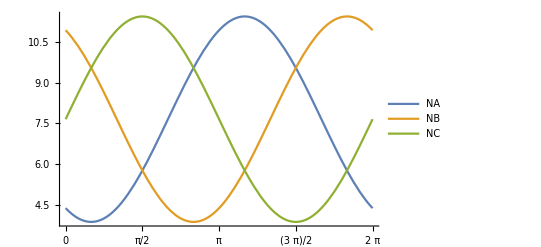

```mathematica
Plot[{NA,NB,NC},{φ,0,2 π},PlotLegends->"Expressions",Ticks->{Range[0,2 Pi,Pi/4],Automatic}]
```

Dangerous orientations

```mathematica
DA=(φ/.FindRoot[D[NA,φ]==0,{φ,π/4}]) 180/π
DB=(φ/.FindRoot[D[NB,φ]==0,{φ,3 π/4}]) 180/π
DC=(φ/.FindRoot[D[NC,φ]==0,{φ,6π/4}]) 180/π
```

30.

150.

270.